## Results

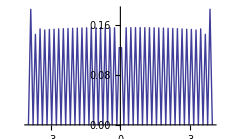
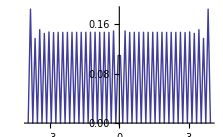
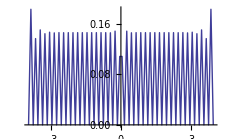
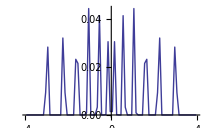
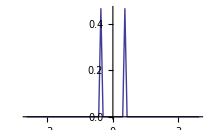
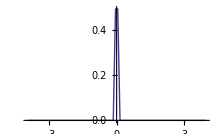
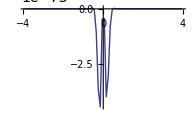
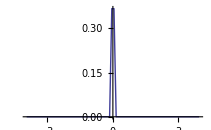
```mathematica
-Graphics- -Graphics-  -Graphics-
(*disperal=.5, sigmac=1*)                   (*dispersal=.5, sigmac=5*)           (*dispersal=.5, sigmac=20*)
-Graphics--Graphics-    -Graphics-
     (*dispersal=10, sigmac=1*)       (*disperal=10, sigmac=5*)          (*dispersal=10, sigmac=20*)
-Graphics--Graphics--Graphics-
(*dispersal=20,sigmac=1*)(*dispersal=20, sigmac=5*)(*disperal=20, sigmac=20*)
```

We first explored a species sorting set-up with a dispersal of 0 with a sigma-c at 1 and found that many species were able to coexist in their optimal environment. As we raised the dispersal to .5, many species were still able to coexist because of the low dispersal rate. However, when we raised the dispersal rate to 10, the number of species able to coexist started to decrease to 12 patches with possibly multiple species. Finally, when dispersal rate was raised to 20, no species were able to survive because there was too much “leakage” from their optimal environment. The graph shown is a Mathematica artifact of very small numbers being found and zoomed in on. 

Next, we varied sigma-c, the tolerance of each species for the environmental variable. As we increased sigma-c at low dispersal rates, the coexistance was not affected. At intermediate dispersal rates, the number of species coexisting went down. This is because there was more competition between species both through dispersal and wider niches. At high dispersal rates, the higher sigma-c values allowed one species to survive the dispersal amounts.

## model

```mathematica
c[y_,yopt_]:=cmax; (*growth rates, choose one, sigmac is how your competitive ability falls off away from optimum*)
c[y_,yopt_]:=cmax*E^(-(y-yopt)^2/(2*σc^2));
 (*mortality rates, choose one*)
m[y_,yopt_]:=mmin;
m[y_,yopt_]:=mmin+σm*(y-yopt)^2;



praw[y_]:=1/Sqrt[2*Pi*σe^2]*E^(-y^2/(2*σe^2)); (*probablity of having different patches, choose one*)
praw[y_]:=1;
```

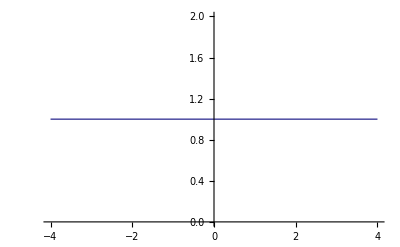

```mathematica
σe=1.0; (*smaller-> sharper peaked*)
Plot[praw[y],{y,-4,4},PlotRange->All]
```

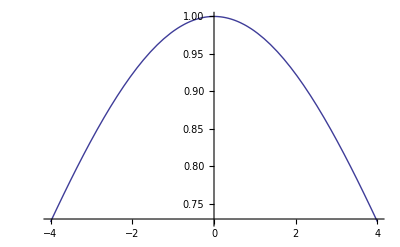

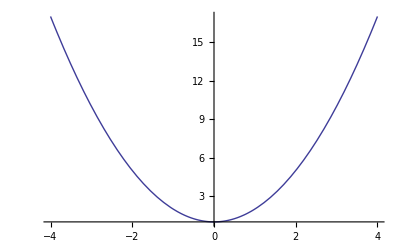

```mathematica
cmax=1;
mmin=1;
σc=5.0;
σm=1.0;
Plot[c[y,0],{y,-4,4},PlotRange->All]
Plot[m[y,0],{y,-4,4},PlotRange->All]
```

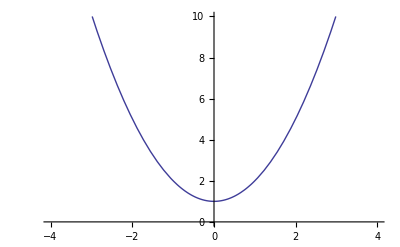

```mathematica
Plot[m[y,0]/c[y,0],{y,-4,4},PlotRange->{0,10}] (*environment type 0*)
```

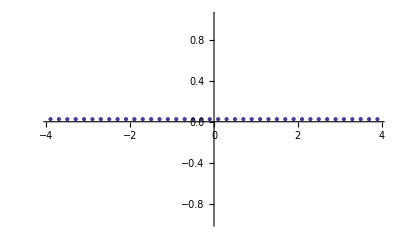

-Graphics- -Graphics- -Graphics-

-Graphics- -Graphics- -Graphics-

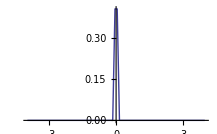
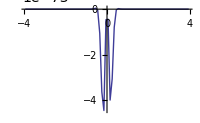

```mathematica
nsp=80;
nx=40;

Do[
rin[x]=10;(*nutrient supply*)
y[x]=-4+8*(x-0.5)/nx;(*defining patches*)
,{x,1,nx}];

pden=Sum[praw[y[x]],{x,1,nx}];

Do[
p[x]=praw[y[x]]/pden;
,{x,1,nx}]

ListPlot[Table[{y[x],p[x]},{x,1,nx}],PlotRange->All](*initializing species*)

Do[
yopt[i]=-4+8*(i-0.5)/nsp;
,{i,1,nsp}];

a=1;(*chemostat flowthrough rate, leave it*)
d=20;(*dispersal rate, change it around*)
   

cmax=1;
σe=1.0;
σ=1.0;
mmin=1.0;

tmaxold=tmax;
tmax=10^9;

eqns=Flatten[Join[
Table[
n[i,x]'[t]==c[y[x],yopt[i]]*r[x][t]*n[i,x][t]-m[y[x],yopt[i]]*n[i,x][t]-d*n[i,x][t]+Sum[d*n[i,x′][t]*p[x′],{x′,1,nx}]
,{i,1,nsp},{x,1,nx}],
Table[r[x]'[t]==a*(rin[x]-r[x][t])-Sum[c[y[x],yopt[i]]*r[x][t]*n[i,x][t],{i,1,nsp}],{x,1,nx}]
]];
ics=Flatten[Join[
Table[n[i,x][0]==0.01,{i,1,nsp},{x,1,nx}],
Table[r[x][0]==rin[x],{x,1,nx}]]];(*initial conditions*)
(*
ics=Flatten[Join[
Table[n[i,x][0]==Evaluate[n[i,x][tmaxold]/.sol[[1]]],{i,1,nsp},{x,1,nx}],
Table[r[x][0]==Evaluate[r[x][tmaxold]/.sol[[1]]],{x,1,nx}]]];
*)
unks=Flatten[Join[
Table[n[i,x],{i,1,nsp},{x,1,nx}],
Table[r[x],{x,1,nx}]]];(*what we're solving for*)

sol=NDSolve[Flatten[Join[eqns,ics]],unks,{t,0,tmax},AccuracyGoal->4];(*NDsolve for a looooooong time*)
```

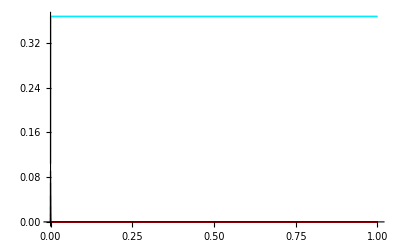

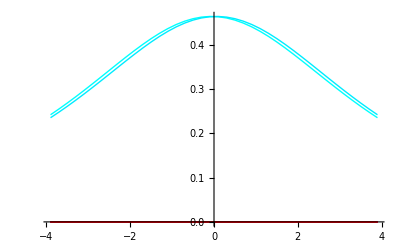

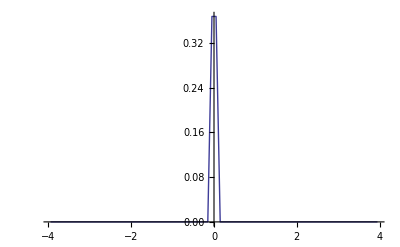

```mathematica
Plot[Evaluate[Table[Sum[n[i,x][t]*p[x],{x,1,nx}],{i,1,nsp}]/.sol],{t,0,tmax}, PlotStyle->Table[Hue[i/nsp],{i,1,nsp}],PlotRange->All] (*time dynamics of every species across all patches*)
(*with dispersal, competitive exclusion occurs*)

ListPlot[Table[Table[{y[x],n[i,x][tmax]/.sol[[1]]},{x,1,nx}],{i,1,nsp}],Joined->True,PlotStyle->Table[Hue[i/nsp],{i,1,nsp}],PlotRange->All] (*x is environmental parameter, each colored line is a different species, equilibrium abundance across time, showing that each species has one patch that it lives and excluded everywhere else in species sorting*)
(*with dispersal, species are specilizing in areas*)

ListPlot[Table[{yopt[i],Sum[n[i,x][tmax]*p[x]/.sol[[1]],{x,1,nx}]},{i,1,nsp}],PlotRange->All,PlotStyle->PointSize[0.012],Joined->True](*integrated biomass, species success y axis vs optimum environment, trait axis, x axis*)(*with dispersal, end with only eight clumps with a couple species co-existing*)
```

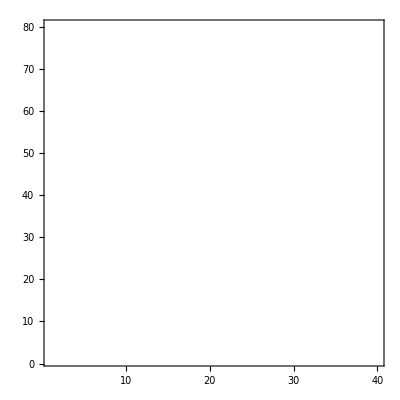

```mathematica
ListDensityPlot[Table[n[i,x][tmax]/.sol[[1]],{i,1,nsp},{x,1,nx}],Mesh->False,ColorFunction->(GrayLevel[1-#]&),PlotRange->All] (*species number on y, patches types on x, darkness is abundance*)
```

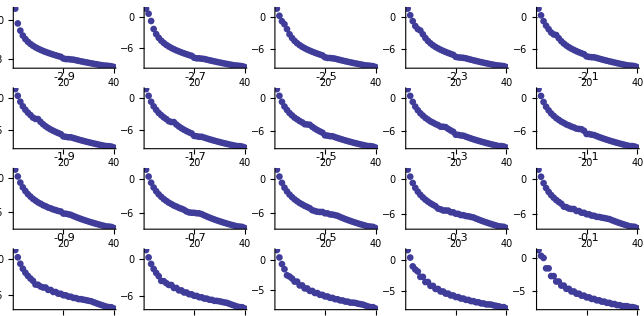

```mathematica
ncolumns=5;
nrows=nx/ncolumns/2;
Do[
raplot[x]=ListPlot[Sort[Log[2,Select[Table[n[i,x][tmax]/.sol[[1]],{i,1,nsp}],#>10^-10&]],Greater],PlotStyle->PointSize[0.012],PlotRange->All,PlotLabel->y[x],DisplayFunction->Identity];
,{x,1,nx/2}]

Show[GraphicsGrid[Table[raplot[ncolumns*row+column],{row,0,nrows-1},{column,1,ncolumns}]]](*within a given patch, species rank and log abundance*)
```

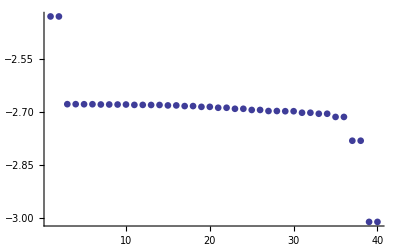

```mathematica
ListPlot[Sort[Log[2,Select[Table[Sum[n[i,x][tmax]*p[x]/.sol[[1]],{x,1,nx}],{i,1,nsp}],#>10^-10&]],Greater],PlotRange->All,PlotStyle->PointSize[0.012]](*same thing as above, summed across the landscape*)
```

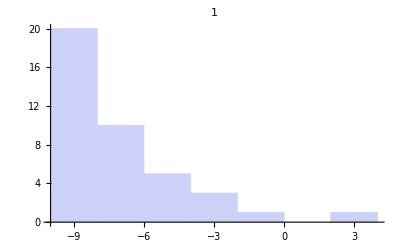

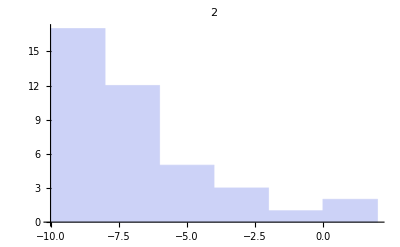

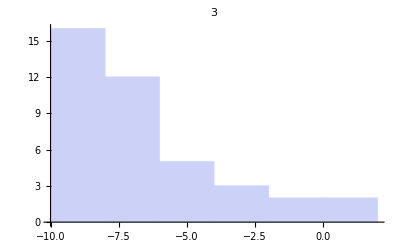

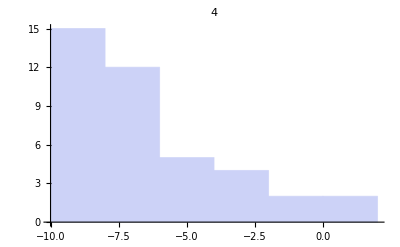

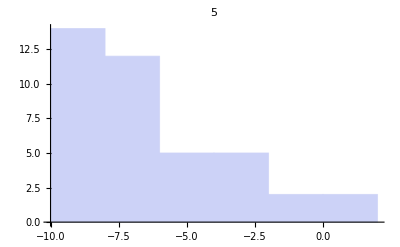

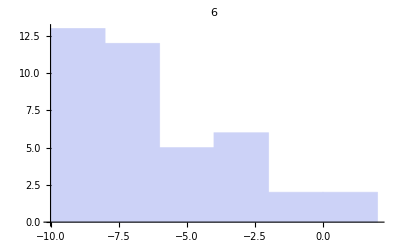

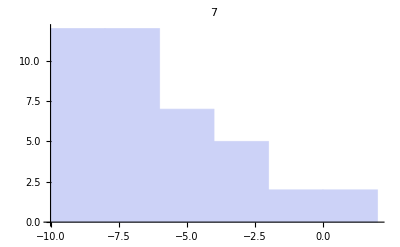

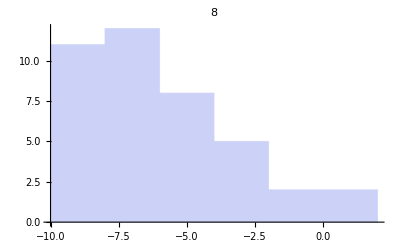

```mathematica
Do[
Print[Histogram[Log[2,Select[Table[n[i,x][tmax]/.sol[[1]],{i,1,nsp}],#>10^-10&]],{2},PlotLabel->x]];
,{x,1,nx/2}];
```